# Time complexity analysis of a recursive DFS-based percolation algorithm

Daniel García Solla

## Initial functions

```mathematica
p=0.96
f[x_,y_]:=(p^Abs[x])*(p^Abs[y])
Plot3D[f[x,y],{x,-50,50},{y,-50,50}, PlotRange->{0,1}, ColorFunction->"AvocadoColors"]
```

0.96

-Graphics3D-

```mathematica
f2[x_,y_]:=p^(Abs[x]+Abs[y]+Abs[x+y]+Abs[y-x])
Plot3D[f2[x,y],{x,-50,50},{y,-50,50}, PlotRange->{0,1}, ColorFunction->"AvocadoColors",  PlotPoints->300]
```

-Graphics3D-

```mathematica
f3[x_,y_,z_]:=p^(Abs[x]+Abs[y]+Abs[z]+Abs[x+y]+Abs[y+z]+Abs[x+z]+Abs[x+y+z]+Abs[-x+y+z]+Abs[x-y+z]+Abs[x+y-z]+Abs[-x-y+z]+Abs[x-y-z]+Abs[-x+y-z]+Abs[-x-y-z])
Plot3D[f3[x,y, 0],{x,-50,50},{y,-50,50},PlotRange->{0,1},ColorFunction->"AvocadoColors",PlotPoints->300, ImageSize->Large]
```

-Graphics3D-

```mathematica
DensityPlot[f3[x,y,15],{x,-10,10},{y,-10,10},PlotRange->All,AxesLabel->{"x","y","z"},PlotLabel->"3D Plot of f3"]
ContourPlot3D[f3[x,y,z],{x,-10,10},{y,-10,10},{z,-10,10},Contours->{0.5},PlotRange->All,AxesLabel->{"x","y","z"},PlotLabel->"Contour Plot of f3"]
```

-Graphics-

-Graphics3D-

```mathematica
Plot3D[f[x,y],{x,0,50},{y,0,50}, PlotRange->{0,1}, ColorFunction->"AvocadoColors"]
Plot3D[f2[x,y],{x,0,50},{y,0,50}, PlotRange->{0,1}, ColorFunction->"AvocadoColors", PlotPoints->300]
```

-Graphics3D-

-Graphics3D-

Expected number of elements at x iteration

```mathematica
b[x_]:=n(1-(1-(1/n))^x);
```

## Calculate area under axis section (1D case)

```mathematica
Clear[p];
Integrate[f[x,0],{x,-Infinity,Infinity}]
Integrate[f2[x,0],{x,-Infinity,Infinity}]
Integrate[f2[x,0],{x,-Infinity,Infinity}, p]
```

Piecewise[{{-2/Log[p], Re[Log[p]]<0}, {Integrate[p^Abs[x],{x,-∞,∞},Assumptions→Re[Log[p]]≥0], True}}]

Piecewise[{{-2/(3 Log[p]), Re[Log[p]]<0}, {Integrate[p^(3 Abs[x]),{x,-∞,∞},Assumptions→Re[Log[p]]≥0], True}}]

ConditionalExpression[-2/3 ExpIntegralEi[Log[p]], Re[Log[p]]≤0]

```mathematica
Integrate[-2/(3Log[p]), p]
```

-(2 LogIntegral[p])/3

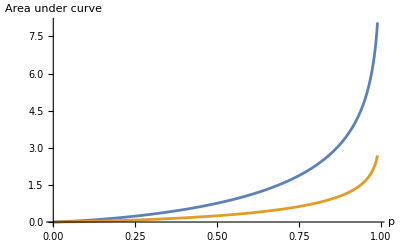

```mathematica
Plot[{-2LogIntegral[p], (-2/3)LogIntegral[p]},{p,0,0.99},PlotRange->All,AxesLabel->{"p","Area under curve"}]
```

### Calculate n exponent

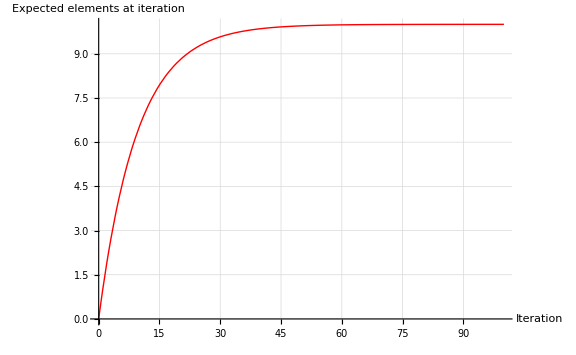

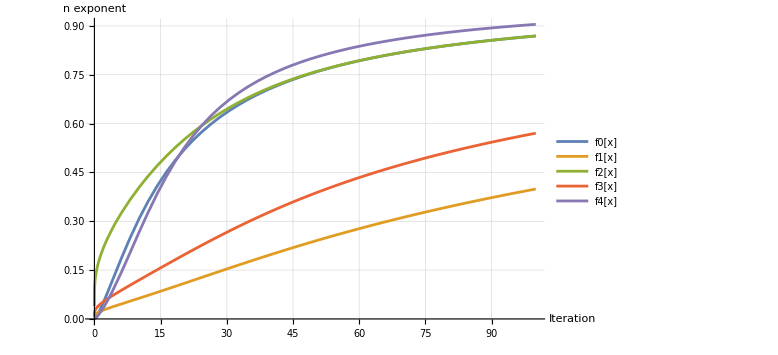

```mathematica
n=10;
b[x_]:=n(1-(1-(1/n))^x);
g[x_]:=(-2/3)LogIntegral[x]
nexp0[x_]:=1*(g[b[x]/n])/(g[b[x]/n]+1)
nexp1[x_]:=1*(g[b[x]/n])/(g[b[x]/n] +b[x])
nexp2[x_]:=1*(g[b[x]/n])/(g[b[x]/n] +b[x]/n)
nexp3[x_]:=1*(g[b[x]/n])/(g[b[x]/n] +b[x]/2)
nexp4[x_]:=2/Pi *ArcTan[g[b[x]/n]]
Plot[{b[x]},{x,0,10*n},PlotRange->All, PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}},AxesLabel->{"Iteration","Expected elements at iteration"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
Plot[{nexp0[x], nexp1[x], nexp2[x], nexp3[x], nexp4[x]},{x,0, 10*n },PlotRange->All,AxesLabel->{"Iteration","n exponent"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}, PlotLegends->{"f0[x]","f1[x]","f2[x]","f3[x]","f4[x]"}]
```

### Calculate insertion complexity

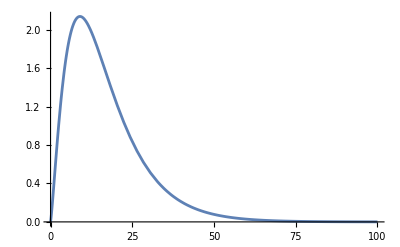

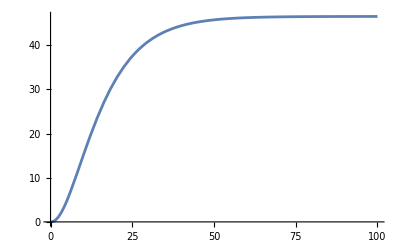

(4 (-1+n)^x n^(1-x) LogIntegral[1-((-1+n)/n)^x])/(-3+2 LogIntegral[1-((-1+n)/n)^x])

4 ∫((-1+n)^x n^(1-x) LogIntegral[1-((-1+n)/n)^x])/(-3+2 LogIntegral[1-((-1+n)/n)^x])ⅆx

```mathematica
n=10;
ins[x_]:=(1-b[x]/n)*2 *n*((g[b[x]/n])/(g[b[x]/n]+1))
Plot[{ins[x]},{x, 0, 10n}]
Plot[{NIntegrate[ins[x], {x, 0, q}]},{q, 0, 100}]
Clear[n]
FullSimplify[ins[x]//FunctionExpand]
Integrate[FullSimplify[ins[x]//FunctionExpand],x]
```

### Get the max point

13.3418

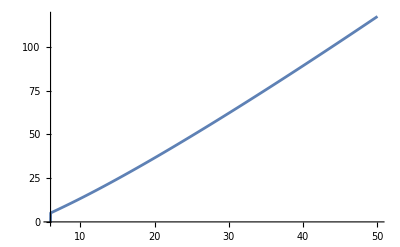

```mathematica
n=10;
puntoEstab:=Module[{result},result=NMaximize[{ins[x], x>0},x];
xOptimal=x/. result[[2]];xOptimal]
puntoEstab
Plot[{puntoEstab},{n, 6, 50}]
(*Plot[{NIntegrate[ins[x], {x, 0, puntoEstab}]},{n, 2, 4}]*)
```

### Sum insertion complexity until the algorithm ends

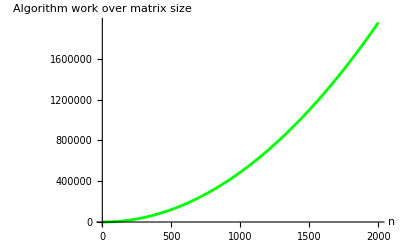

```mathematica
LaunchKernels[];
Clear[n];
points=ParallelTable[{n, NIntegrate[ins[x],{x,0,(n)*HarmonicNumber[n]}, WorkingPrecision->8]},{n, 2, 2000}];
ListLinePlot[{points},PlotRange->All,AxesLabel->{"n","Algorithm work over matrix size"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
CloseKernels[];
```

### Fit the sum points

{-0.8273237,2.016111}

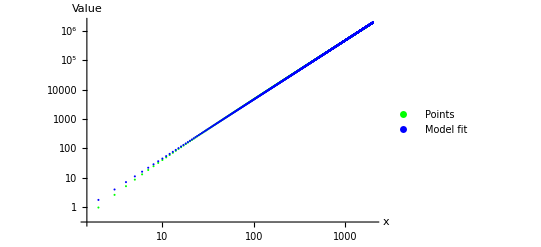

```mathematica
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x, IncludeConstantBasis->True];
fittedLine=linearModel["Function"];
linearModel["BestFitParameters"]
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,2000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right]]
```

FittedModel[…]

0.48242684 #1^2.001856&

| DF | SS | MS
Model | 2 | 1.532913×10^15 | 7.664563×10^14
Error | 1997 | 1.3×10^7 | 6700.
Uncorrected Total | 1999 | 1.532913×10^15 | 
Corrected Total | 1998 | 6.81158×10^14 |

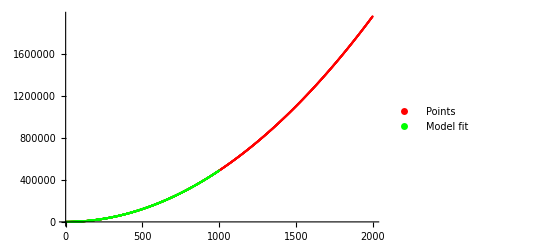

```mathematica
nonlinearModel=NonlinearModelFit[points,a*x^c ,{a,c},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,1000}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right]]
```

### Distribution of iterations before process ends

60

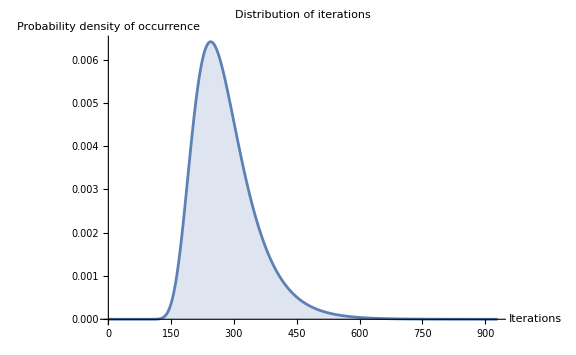

245

280.792

```mathematica
n=60
distr[i_]:=(Factorial[n]/(n^i))*StirlingS2[i-1,n-1]
iValues=Range[1,2 n^1.5,1];
maxIndex=First@Ordering[Table[distr[i],{i,iValues}],-1];
DiscretePlot[{distr[i]},{i,iValues},AxesLabel->{"Iterations","Probability density of occurrence"},PlotLabel->"Distribution of iterations",PlotRange->Full,ImageSize->Large]
maxIndex
N[(n*Sum[1/j,{j,1,n}])]
```

Approach the Coupon Collector Problem distribution (m=1)

{Piecewise[{{n^-k n! StirlingS2[k,n], k≥n}, {0, True}}],Piecewise[{{n^-k n! (-n StirlingS2[-1+k,n]+StirlingS2[k,n]), k≥1+n}, {n^-k n! StirlingS2[k,n], k≥n}, {0, True}}]}

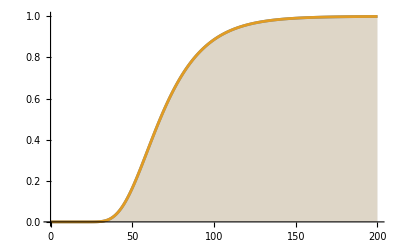

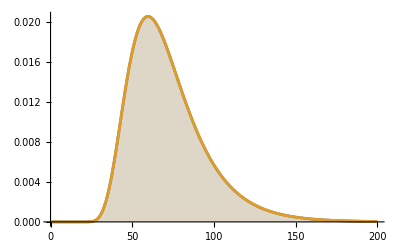

```mathematica
Clear[n]
b[x_]:=n*(1-(1-(1/n))^x)
p[k_,j_,n_,m_]:=StirlingS2[k,j]*Factorial[n*m]/(Factorial[(n*m)-j]*(n*m)^k)
ratio[n_,k_]:=Sum[p[k,j,n,1]*KroneckerDelta[n,j]/Binomial[n,Min[n,j]]//FullSimplify,{j,1,k}]
distr[n_,k_]:=ratio[n,k]-ratio[n,k-1]
FullSimplify[{ratio[n,k],distr[n,k]},Assumptions->{n∈PositiveIntegers,k∈PositiveIntegers}]
n=20;
DiscretePlot[{(Factorial[n]/(n^k))*StirlingS2[k,n],ratio[n,k]},{k,0,200}]
DiscretePlot[{(Factorial[n]/(n^k))*StirlingS2[k-1,n-1],distr[n,k]},{k,0,200}]
```

Calculate mean of m=1 distribution😋

```mathematica
Clear[n]
FullSimplify[Sum[Sum[(Factorial[n]/(n^x))*((1/(n-1)!)*(-1)^(j+n-1)  Binomial[n-1,j]  j^(x-1))*x//FullSimplify,{x,0,Infinity}]//FunctionExpand,{j,0,n-1}],Assumptions->{n∈PositiveIntegers}]
```

n HarmonicNumber[n]

```mathematica
Clear[n]
FunctionExpand[Binomial[n,b[k]]]
FullSimplify[FunctionExpand[distr[x,k]]]
DiscretePlot3D[Gamma[1+n]/(Gamma[1+n-(-1+n)^k n^(1-k)] Gamma[1+(-1+n)^k n^(1-k)]),{k,1,70},{n,40,50},ImageSize->Medium]
```

Gamma[1+n]/(Gamma[1+n-(-1+n)^k n^(1-k)] Gamma[1+(-1+n)^k n^(1-k)])

1/Gamma[1+k]n^-k Gamma[1+k+(-1+((-1+n)/n)^k) n] Gamma[1+n-(-1+n)^k n^(1-k)] (n^k (-HarmonicNumber[k]+HarmonicNumber[k+(-1+((-1+n)/n)^k) n])+(-1+n)^k n (HarmonicNumber[k+(-1+((-1+n)/n)^k) n]-HarmonicNumber[n-(-1+n)^k n^(1-k)]) (Log[-1+n]-Log[n]))

-Graphics3D-

## Calculate volume under the functions (square 2D case)

```mathematica
Clear[p];
Integrate[f[x,y],{x,0,Infinity},{y,0,Infinity}, p]
Integrate[f2[x,y],{x,-Infinity,0},{y,-Infinity,0}]
```

ConditionalExpression[-p/Log[p]+LogIntegral[p], Log[p]≤0]

Piecewise[{{1/(6 Log[p]^2), Re[Log[p]]<0}, {Integrate[p^(Abs[x]+Abs[y]+Abs[-x+y]+Abs[x+y]),{x,-∞,0},{y,-∞,0},Assumptions→Re[Log[p]]≥0], True}}]

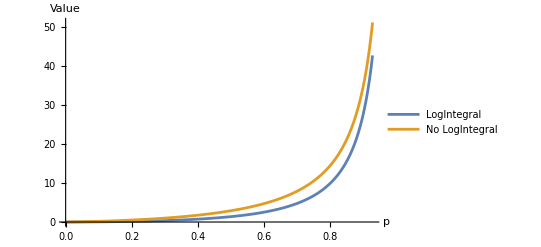

```mathematica
Plot[{4 (-p/Log[p]+LogIntegral[p]), 4 (-p/Log[p])},{p,0,0.93},PlotRange->All,AxesLabel->{"p","Value"}, PlotLegends->{"LogIntegral","No LogIntegral"}]
```

### Calculate n exponent

10

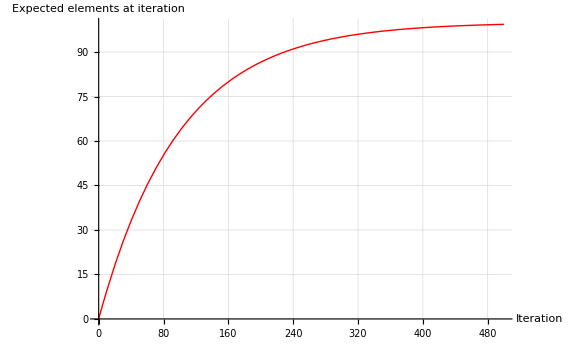

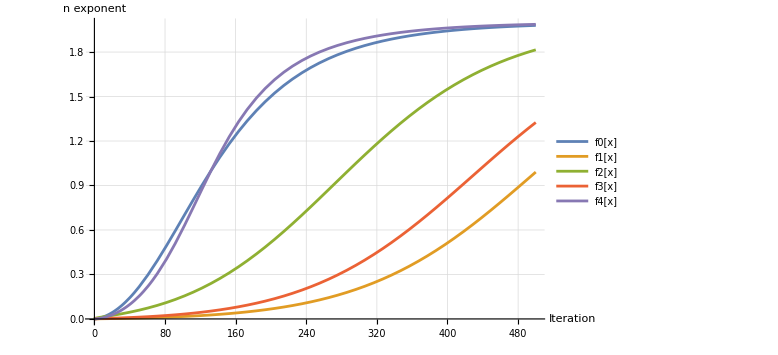

```mathematica
n=10
b[x_]:=(n^2)*(1-(1-(1/n^2))^x);
g[x_]:=(4/6)*(-x/Log[x]+LogIntegral[x])
nexp0[x_]:=2*(g[b[x]/n^2])/(g[b[x]/n^2] +1)
nexp1[x_]:=2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x])
nexp2[x_]:=2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x]/n)
nexp3[x_]:=2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x]/2)
nexp4[x_]:=4/Pi *ArcTan[g[b[x]/n^2]]
Plot[{b[x]},{x,0,5*n^2},PlotRange->All, PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}},AxesLabel->{"Iteration","Expected elements at iteration"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
Plot[{nexp0[x], nexp1[x], nexp2[x], nexp3[x], nexp4[x]},{x,0, 5*n^2 },PlotRange->All,AxesLabel->{"Iteration","n exponent"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}, PlotLegends->{"f0[x]","f1[x]","f2[x]","f3[x]","f4[x]"}]
```

### Calculate insertion complexity

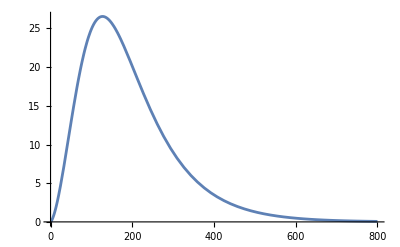

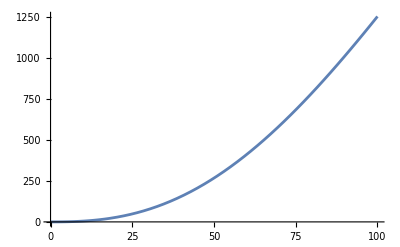

```mathematica
n=10;
ins[x_]:=(1-b[x]/n^2)*2n^(2*(g[b[x]/n^2])/(g[b[x]/n^2] +1))
ins[x_]:=(1-b[x]/n^2)*2(n^2)*((g[b[x]/n^2])/(g[b[x]/n^2] +1))
Plot[{ins[x]},{x, 0, 8n^2}]
Plot[{NIntegrate[ins[x], {x, 0, q}]},{q, 0, 100}]
```

```mathematica
derivative=D[ins[x],x]
```

(1-1/n^2)^x n^((4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/(3 (1+2/3 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x])))) Log[1-1/n^2]+(1-1/n^2)^x n^((4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/(3 (1+2/3 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x])))) Log[n] ((8 (1-1/n^2)^x Log[1-1/n^2] (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/(9 Log[1-(1-1/n^2)^x]^2 (1+2/3 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))^2)-(4 (1-1/n^2)^x Log[1-1/n^2])/(3 Log[1-(1-1/n^2)^x]^2 (1+2/3 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))))

### Get the max point (precision fails😊)

2.26093×10^-9

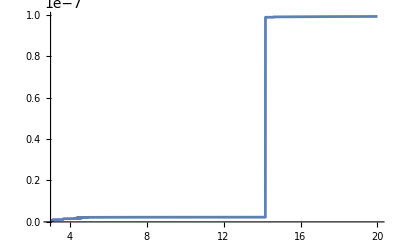

```mathematica
n=10;
puntoEstab:=Module[{result},result=NMaximize[{ins[x], x>0},x];
xOptimal=x/. result[[2]];xOptimal]
puntoEstab
Plot[{puntoEstab},{n, 3, 20}]
```

### Sum insertion complexity until the algorithm ends

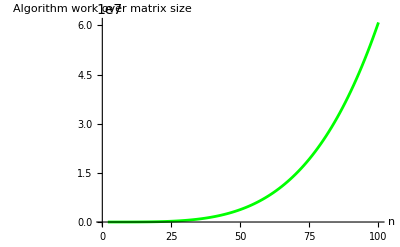

```mathematica
LaunchKernels[];
Clear[n]
points=ParallelTable[{n, NIntegrate[ins[x],{x,0,(n^2)*HarmonicNumber[n^2]}, WorkingPrecision->10]},{n, 2, 100}];
ListLinePlot[{points},PlotRange->All,AxesLabel->{"n","Algorithm work over matrix size"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
CloseKernels[];
```

### Fit the sum points (finally🤝)

{-0.5950398242,4.024615051}

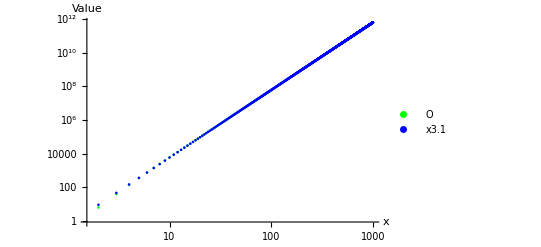

```mathematica
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x];
fittedLine=linearModel["Function"];
linearModel["BestFitParameters"]
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,1000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
```

FittedModel[…]

0.6083444978 #1^4.000341471&

| DF | SS | MS
Model | 2 | 1.63411194×10^18 | 8.17055969×10^17
Error | 147 | 2.11×10^8 | 1.44×10^6
Uncorrected Total | 149 | 1.63411194×10^18 | 
Corrected Total | 148 | 1.03992121×10^18 |

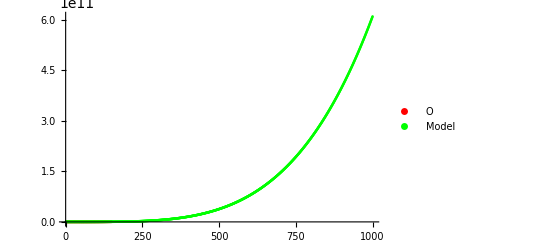

```mathematica
nonlinearModel=NonlinearModelFit[points,a*x^c ,{a,c},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,1000}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"O","Model"}],Right]]
```

### Distribution of iterations before process ends

```mathematica
n=9
distr[i_]:=Binomial[n^2, b[i]]
iValues=Range[1,n^2,1];
maxIndex=First@Ordering[Table[distr[i],{i,iValues}],-1];
DiscretePlot[distr[i],{i,iValues},AxesLabel->{"Iterations","Probability density of occurrence"},PlotLabel->"Distribution of iterations",PlotRange->Automatic,ImageSize->Large]
maxIndex
```

9

-Graphics-

81

## Calculate area under axis section (3D case)

```mathematica
Clear[p];
Integrate[f3[x,y, z],{x,-Infinity,Infinity}, {y,-Infinity,Infinity}, {z,-Infinity,Infinity}]
```

Piecewise[{{2 (Integrate[p^(11 x)/(2 Log[p]^2)-p^(23 x/2)/Log[p]^2+p^(12 x)/(2 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(11 x)/(6 Log[p]^2)-p^(12 x)/(2 Log[p]^2)+p^(25 x/2)/(3 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(11 x)/(6 Log[p]^2)-p^(12 x)/(4 Log[p]^2)+p^(14 x)/(12 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(12 x)/(4 Log[p]^2)-p^(25 x/2)/(3 Log[p]^2)+p^(14 x)/(12 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(12 x)/(60 Log[p]^2)-p^(17 x)/(60 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(12 x)/(50 Log[p]^2)-p^(29 x/2)/(25 Log[p]^2)+p^(17 x)/(50 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(12 x)/(20 Log[p]^2)-p^(14 x)/(12 Log[p]^2)+p^(17 x)/(30 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(12 x)/(28 Log[p]^2)-p^(14 x)/(20 Log[p]^2)+p^(19 x)/(70 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(23 x)/(11 Log[p]^2)-p^(24 x)/(11 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(17 x)/(84 Log[p]^2)-p^(24 x)/(84 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(14 x)/(110 Log[p]^2)-p^(24 x)/(110 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(12 x)/(132 Log[p]^2)-p^(24 x)/(132 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+3 Integrate[p^(12 x)/(60 Log[p]^2)-p^(17 x)/(35 Log[p]^2)+p^(24 x)/(84 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(14 x)/(30 Log[p]^2)-p^(17 x)/(21 Log[p]^2)+p^(24 x)/(70 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(12 x)/(70 Log[p]^2)-p^(17 x)/(70 Log[p]^2)-p^(19 x)/(70 Log[p]^2)+p^(24 x)/(70 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(12 x)/(132 Log[p]^2)-p^(23 x)/(11 Log[p]^2)+p^(24 x)/(12 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(24 x)/(11 Log[p]^2)-p^(25 x)/(11 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(14 x)/(110 Log[p]^2)-p^(24 x)/(10 Log[p]^2)+p^(25 x)/(11 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(14 x)/(98 Log[p]^2)-p^(28 x)/(98 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(24 x)/(60 Log[p]^2)-p^(29 x)/(60 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(17 x)/(84 Log[p]^2)-p^(24 x)/(35 Log[p]^2)+p^(29 x)/(60 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(24 x)/(98 Log[p]^2)-p^(38 x)/(98 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(17 x)/(49 Log[p]^2)-(3 p^(24 x))/(98 Log[p]^2)+p^(38 x)/(98 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[-p^(12 x)/(25 Log[p]^2)+p^(17 x)/(25 Log[p]^2)-(p^(12 x) x)/(5 Log[p]),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[-p^(12 x)/(25 Log[p]^2)+p^(29 x/2)/(25 Log[p]^2)-(p^(12 x) x)/(10 Log[p]),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[-p^(12 x)/(50 Log[p]^2)+p^(17 x)/(50 Log[p]^2)-(p^(12 x) x)/(10 Log[p]),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(23 x/2)/Log[p]^2-p^(12 x)/Log[p]^2+(p^(12 x) x)/(2 Log[p]),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(11 x)/(2 Log[p]^2)-p^(12 x)/(2 Log[p]^2)+(p^(12 x) x)/(2 Log[p]),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(11 x)/Log[p]^2-p^(12 x)/Log[p]^2+(p^(12 x) x)/Log[p],{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[-p^(14 x)/(98 Log[p]^2)+p^(28 x)/(98 Log[p]^2)-(p^(14 x) x)/(7 Log[p]),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[p^(11 x)/(9 Log[p]^2)-p^(14 x)/(9 Log[p]^2)+(p^(14 x) x)/(3 Log[p]),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(12 x)/(132 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(14 x)/(154 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(24 x)/(154 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(24 x)/(132 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]), Re[Log[p]]≥0}, {-386/(17493 Log[p]^3), True}}]

```mathematica
Integrate[-386/(17493 Log[p]^3), p]
```

-(386 (-p/(2 Log[p]^2)-p/(2 Log[p])+LogIntegral[p]/2))/17493

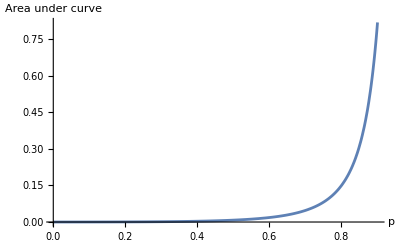

```mathematica
Plot[{-386/17493 (-p/(2 Log[p]^2)-p/(2 Log[p])+LogIntegral[p]/2)},{p,0,0.9},PlotRange->All,AxesLabel->{"p","Area under curve"}]
```

### Calculate n exponent

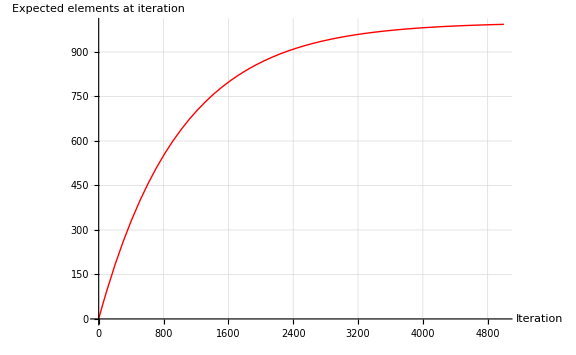

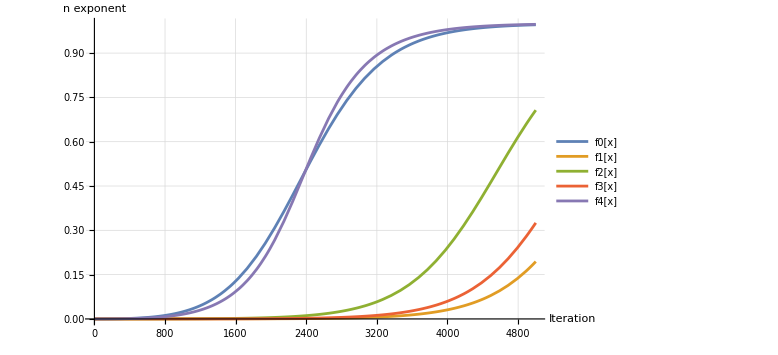

```mathematica
n=10;
b[x_]:=(n^3)*(1-(1-(1/n^3))^x);
g[x_]:=-386/17493 (-x/(2 Log[x]^2)-x/(2 Log[x])+LogIntegral[x]/2)
nexp0[x_]:=1*(g[b[x]/n^3])/(g[b[x]/n^3]+1)
nexp1[x_]:=1*(g[b[x]/n^3])/(g[b[x]/n^3] +b[x])
nexp2[x_]:=1*(g[b[x]/n^3])/(g[b[x]/n^3] +b[x]/n)
nexp3[x_]:=1*(g[b[x]/n^3])/(g[b[x]/n^3] +b[x]/2)
nexp4[x_]:=2/Pi *ArcTan[g[b[x]/n^3]]
Plot[{b[x]},{x,0,5n^3},PlotRange->All, PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}},AxesLabel->{"Iteration","Expected elements at iteration"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
Plot[{nexp0[x], nexp1[x], nexp2[x], nexp3[x], nexp4[x]},{x,0, 5n^3 },PlotRange->All,AxesLabel->{"Iteration","n exponent"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}, PlotLegends->{"f0[x]","f1[x]","f2[x]","f3[x]","f4[x]"}]
```

### Calculate insertion complexity

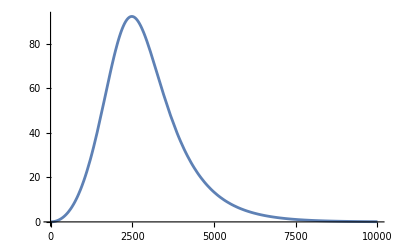

```mathematica
n=10;
ins[x_]:=(1-b[x]/n^3)*2*n^ Nest[Power[((g[b[x]/n^3])/(g[b[x]/n^3]+1)),#]&,((g[b[x]/n^3])/(g[b[x]/n^3]+1)),n-1]
ins[x_]:=(1-b[x]/n^3)*2*n^(3(g[b[x]/n^3])/(g[b[x]/n^3]+1))
ins[x_]:=(1-b[x]/n^3)*2*(n^3)*((g[b[x]/n^3])/(g[b[x]/n^3]+1))
Plot[{ins[x]},{x, 0, n^4}]
```

### Get the max point

```mathematica
n=10;
puntoEstab:=Module[{result},result=NMaximize[{ins[x], x>0},x];
xOptimal=x/. result[[2]];xOptimal]
puntoEstab
Plot[{puntoEstab},{n, 6, 50}]
(*Plot[{NIntegrate[ins[x], {x, 0, puntoEstab}]},{n, 2, 4}]*)
```

13.3418

-Graphics-

### Sum insertion complexity until the algorithm ends

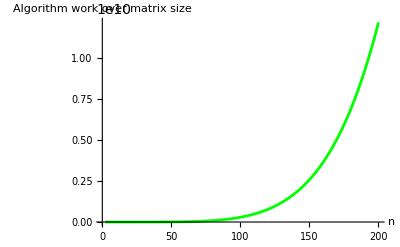

```mathematica
LaunchKernels[];
Clear[n];
points=ParallelTable[{n, NIntegrate[ins[x],{x,0,n^2.8}, WorkingPrecision->20]},{n, 2, 200}];
ListLinePlot[{points},PlotRange->All,AxesLabel->{"n","Algorithm work over matrix size"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
CloseKernels[];
```

### Fit the sum points

{-5.265373560840872756,5.375424488326087646}

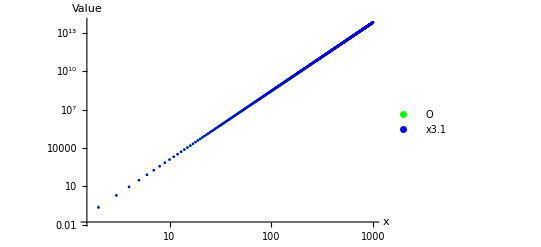

```mathematica
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x];
fittedLine=linearModel["Function"];
linearModel["BestFitParameters"]
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,1000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
```

```mathematica
nonlinearModel=NonlinearModelFit[points,a*x^c ,{a,c},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,1000}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"O","Model"}],Right]]
```

FittedModel[…]

0.1769655601 #1^5.644004954&

| DF | SS | MS
Model | 2 | 2.63735288×10^10 | 1.31867644×10^10
Error | 8 | 162809. | 20351.1
Uncorrected Total | 10 | 2.63736916×10^10 | 
Corrected Total | 9 | 1.77241825×10^10 |

-Graphics-

### Distribution of iterations before process ends

10

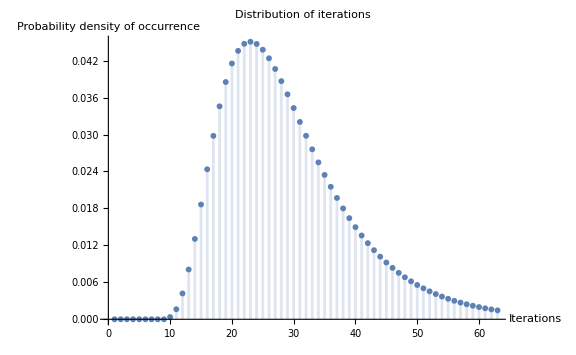

23

29.2897

```mathematica
n=10
distr[i_]:=(Factorial[n]/(n^i))*StirlingS2[i-1,n-1]
iValues=Range[1,2 n^1.5,1];
maxIndex=First@Ordering[Table[distr[i],{i,iValues}],-1];
DiscretePlot[distr[i],{i,iValues},AxesLabel->{"Iterations","Probability density of occurrence"},PlotLabel->"Distribution of iterations",PlotRange->Automatic,ImageSize->Large]
maxIndex
N[(n*Sum[1/j,{j,1,n}])]
```

## Combinatorics

### Simple cases😌

```mathematica
f[n_]:=Binomial[2n,2n-2]-n*Binomial[2n-2,0]
f1[n_]:=Binomial[2n,2n-3]-n*Binomial[2n-2,1]
f2[n_]:=Binomial[2n,2n-4]-n*(Binomial[2n-2,2])+Binomial[n,2]
f3[n_]:=Binomial[2n,2n-5]-n*(Binomial[2n-2,3])+Binomial[n,2]*Binomial[2n-4,1]
f4[n_]:=(4/45)(-5+n)(-4+n)(-3+n) (-2+n) (-1+n)n
f5[n_]:=(8/315)(-6+n)(-5+n)(-4+n)(-3+n) (-2+n) (-1+n)n
f6[n_]:=(2/315)(-7+n)(-6+n)(-5+n)(-4+n)(-3+n) (-2+n) (-1+n)n
FactorTerms[FunctionExpand[{f[x],f1[x],f2[x],f3[x],f4[x],f5[x], f6[x]}]]
Table[{f6[i],f5[i],f4[i],f3[i],f2[i],f1[i], f[i], 2i, 1}, {i, 2, 10}]
```

{2 (-x+x^2),4/3 (2 x-3 x^2+x^3),2/3 (-6 x+11 x^2-6 x^3+x^4),4/15 (24 x-50 x^2+35 x^3-10 x^4+x^5),4/45 (-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6),8/315 (720 x-1764 x^2+1624 x^3-735 x^4+175 x^5-21 x^6+x^7),2/315 (-5040 x+13068 x^2-13132 x^3+6769 x^4-1960 x^5+322 x^6-28 x^7+x^8)}

{{0,0,0,0,0,0,4,4,1},{0,0,0,0,0,8,12,6,1},{0,0,0,0,16,32,24,8,1},{0,0,0,32,80,80,40,10,1},{0,0,64,192,240,160,60,12,1},{0,128,448,672,560,280,84,14,1},{256,1024,1792,1792,1120,448,112,16,1},{2304,4608,5376,4032,2016,672,144,18,1},{11520,15360,13440,8064,3360,960,180,20,1}}

### Closed form for 2 columns (m=2) case

```mathematica
Clear[n]
g[n_]:=Sum[Mod[Binomial[n,i],2],{i,0,n}]
g[n_]:=(2^n)/GCD[2^n,Factorial[n]]
d[n_]:=Factorial[n]/GCD[2^n,Factorial[n]]
f[n_,k_]:=(g[k]/d[k])*Sum[((StirlingS1[k,i])*n^i),{i,0,k}]
Table[f[10,2*10-x], {x,0,2*10}]
FullSimplify[f[n,k]]
```

{0,0,0,0,0,0,0,0,0,0,1024,5120,11520,15360,13440,8064,3360,960,180,20,1}

(2^k FactorialPower[n,k])/(k!)

```mathematica
Clear[n]
b[x_]:=(2*n)*(1-(1-(1/(2*n)))^x)
f[n_,k_]:=(2^k FactorialPower[n,k])/(k!)
p[k_,j_,n_,m_]:=StirlingS2[k,j]*Factorial[n*m]/(Factorial[(n*m)-j]*(n*m)^k)
ratio[n_,k_]:=Sum[p[k,j,n,2]*f[n,2*n-j]/Binomial[n*2,Min[n*2,j]]//FullSimplify,{j,1,k}]
distr[n_,k_]:=ratio[n,k]-ratio[n,k-1]
```

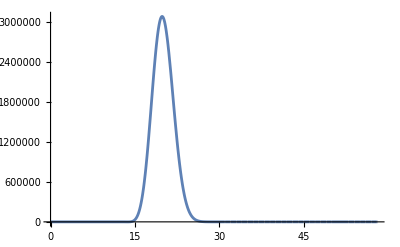

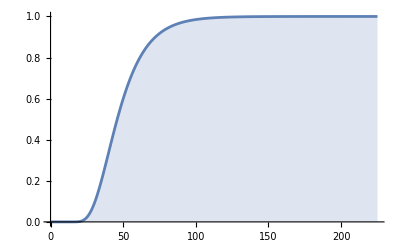

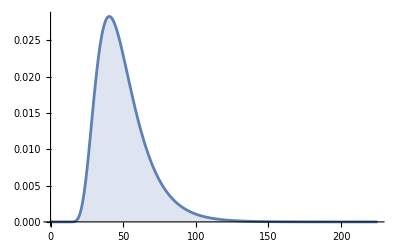

```mathematica
n=15;
Plot[f[n,2n-k], {k, 0, n^1.5}, PlotRange->Full]
DiscretePlot[ratio[n,k],{k,0,n^2}]
DiscretePlot[distr[n,k],{k,0,n^2}]
```

### m=5

```mathematica
f[n_]:=Binomial[5n,5n-2]
f1[n_]:=Binomial[5n,5n-3]
f2[n_]:=Binomial[5n,5n-4]
f3[n_]:=Binomial[5n,5n-5]-n*(Binomial[5n-5,0])
f4[n_]:=Binomial[5n,5n-6]-n*(Binomial[5n-5,1])-6(n-1)
f5[n_]:=Binomial[5n,5n-7]-n*(Binomial[5n-5,2])-2*(n-2)*(Binomial[3,2]+3)-2*(n-1)*((5n-8)+2(5n-7))-2*(n-1)
f6[n_]:=Binomial[5n,5n-8]-n*(Binomial[5n-5,3])
FactorTerms[FunctionExpand[{f[x],f1[x],f2[x],f3[x],f4[x], f5[x], f6[x]}]]
Table[{f6[i],f5[i],f4[i],f3[i],f2[i],f1[i], f[i], 5i, 1}, {i, 2, 10}]
```

{5/2 (-x+5 x^2),5/6 (2 x-15 x^2+25 x^3),5/24 (-6 x+55 x^2-150 x^3+125 x^4),125/24 (-2 x^2+7 x^3-10 x^4+5 x^5),1/144 (864-264 x+650 x^2-5625 x^3+10625 x^4-9375 x^5+3125 x^6),(-18144+46080 x-11340 x^2+28000 x^3-91875 x^4+109375 x^5-65625 x^6+15625 x^7)/1008,(25 (11088 x-26148 x^2+11060 x^3+27125 x^4-49000 x^5+40250 x^6-17500 x^7+3125 x^8))/8064}

{{25,82,194,250,210,120,45,10,1},{6075,6192,4963,3000,1365,455,105,15,1},{124150,76842,38682,15500,4845,1140,190,20,1},{1075875,479282,176976,53125,12650,2300,300,25,1},{5839125,2033262,593595,142500,27405,4060,435,30,1},{23507400,6720407,1622914,324625,52360,6545,595,35,1},{76852325,18637342,3838058,658000,91390,9880,780,40,1},{215464275,45370692,8144652,1221750,148995,14190,990,45,1},{536736750,99872082,15890196,2118750,230300,19600,1225,50,1}}

```mathematica
Table[{ Numerator[2^n/Factorial[n]], Denominator[5^n/Factorial[n]]},{n,0,10}]
```

{{1,1},{2,1},{2,2},{4,6},{2,24},{4,24},{4,144},{8,1008},{2,8064},{4,72576},{4,145152}}

### m=4

```mathematica
f[n_]:=Binomial[4n,4n-2]
f1[n_]:=Binomial[4n,4n-3]
f2[n_]:=Binomial[4n,4n-4]-n*(Binomial[4n-4,0])
f3[n_]:=Binomial[4n,4n-5]-n*(Binomial[4n-4,1])-4(n-1)
f4[n_]:=Binomial[4n,4n-6]-n*(Binomial[4n-4,2])-6*(n-2)-2*(n-1)*((n*4-7)+(n*4-6))
f5[n_]:=Binomial[4n,4n-7]-n*(Binomial[4n-4,3])
f6[n_]:=Binomial[4n,4n-8]-n*(Binomial[4n-4,4])+Binomial[n,2]
FactorTerms[FunctionExpand[{f[x],f1[x],f2[x],f3[x],f4[x], f5[x], f6[x]}]]
Table[{f6[i],f5[i],f4[i],f3[i],f2[i],f1[i], f[i], 4i, 1}, {i, 2, 10}]
```

{2 (-x+4 x^2),4/3 (x-6 x^2+8 x^3),2/3 (-3 x+11 x^2-24 x^3+16 x^4),4/15 (15+3 x-40 x^2+70 x^3-80 x^4+32 x^5),2/45 (-315+570 x+182 x^2-630 x^3+680 x^4-480 x^5+128 x^6),8/315 (810 x-2163 x^2+2387 x^3-1890 x^4+1400 x^5-672 x^6+128 x^7),2/315 (-5670 x+17643 x^2-22078 x^3+16009 x^4-9520 x^5+5152 x^6-1792 x^7+256 x^8)}

{{0,0,10,44,68,56,28,8,1},{288,624,790,760,492,220,66,12,1},{10896,10560,7618,4308,1816,560,120,16,1},{116880,74720,37926,15408,4840,1140,190,20,1},{706416,339264,133082,42364,10620,2024,276,24,1},{3033744,1169872,374262,98088,20468,3276,378,28,1},{10354528,3339648,902418,201124,35952,4960,496,32,1},{29936736,8303040,1942342,376672,58896,7140,630,36,1},{76315680,18572160,3830826,657612,91380,9880,780,40,1}}

{0,0,0,0,0,0,0,0,0,0,1024,1280,640,160,20,1}

(4^(4 n-4 n (1-4^-k n^-k (-1+4 n)^k)) Gamma[1+n] Gamma[1+4 n-4^(1-k) n^(1-k) (-1+4 n)^k])/(Gamma[1+4 n] Gamma[1+n-4^(1-k) n^(1-k) (-1+4 n)^k])

-(4^(-k+4^(1-k) n^(1-k) (-1+4 n)^k) n^-k (-1+4 n)^k Gamma[1+n] Gamma[1+4 n (1-4^-k n^-k (-1+4 n)^k)] (HarmonicNumber[n-4^(1-k) n^(1-k) (-1+4 n)^k]-HarmonicNumber[4 n (1-4^-k n^-k (-1+4 n)^k)]+Log[4]) (Log[4 n]-Log[-1+4 n]))/(Gamma[4 n] Gamma[1+n-4^(1-k) n^(1-k) (-1+4 n)^k])

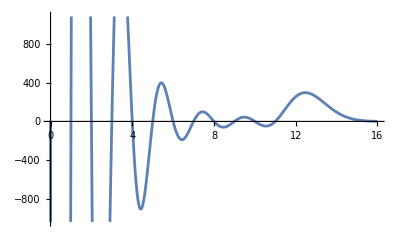

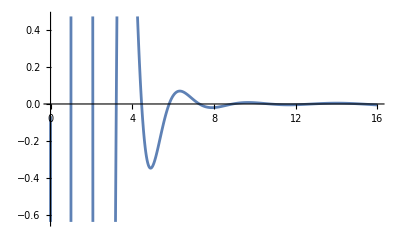

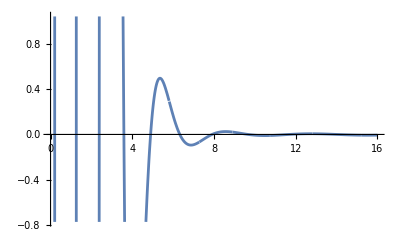

```mathematica
b[x_]:=(4*n)*(1-(1-(1/(4*n)))^x)
f[n_,k_]:=(4^k FactorialPower[n,k])/(k!)
Table[f[5,3*5-x], {x,0,3*5}]
ratio[n_,k_]:=f[n,(4*n)-b[k]]/Binomial[4*n,b[k]]
distr[n_,k_]:=D[ratio[n,x], x]/.x->k
Clear[n]
FactorTerms[FunctionExpand[ratio[n,k]]]
FullSimplify[FunctionExpand[distr[n,k]]]
n=4;
Plot[f[n,4n-k], {k, 0, n^2}]
Plot[ratio[n,k],{k,0,n^2}]
Plot[distr[n,k],{k,0,n^2}]
```

### m=3

```mathematica
f[n_]:=Binomial[3n,3n-2]
f1[n_]:=Binomial[3n,3n-3]-n*Binomial[3n-3,0]
f2[n_]:=Binomial[3n,3n-4]-n*(Binomial[3n-3,1])-2(n-1)
f3[n_]:=Binomial[3n,3n-5]-n*(Binomial[3n-3,2])-6 (n-2)*(n-1)-2(n-2)
f4[n_]:=Binomial[3n,3n-6]-n*(Binomial[3n-3,3])+Binomial[n,2]-20(n-2)
f5[n_]:=Binomial[3n,3n-7]-n*(Binomial[3n-3,4])
f6[n_]:=Binomial[3n,3n-8]-n*(Binomial[3n-3,5])
FactorTerms[FunctionExpand[{f[x],f1[x],f2[x],f3[x],f4[x],f5[x], f6[x]}]]
Table[{f6[i],f5[i],f4[i],f3[i],f2[i],f1[i], f[i], 3i, 1}, {i, 2, 10}]
```

{3/2 (-x+3 x^2),9/2 (-x^2+x^3),1/8 (16+2 x+9 x^2-54 x^3+27 x^4),1/40 (-320+424 x+30 x^2+135 x^3-270 x^4+81 x^5),1/80 (3200-880 x-1566 x^2+765 x^3+405 x^4-405 x^5+81 x^6),3/560 (-2720 x+7392 x^2-6706 x^3+1575 x^4+945 x^5-567 x^6+81 x^7),(3 (30800 x-98460 x^2+118468 x^3-62013 x^4+7560 x^5+5670 x^6-2268 x^7+243 x^8))/4480}

{{0,0,0,0,7,18,15,6,1},{-9,-9,7,67,104,81,36,9,1},{-9,288,554,608,453,216,66,12,1},{2475,3960,3855,2595,1297,450,105,15,1},{25740,23634,15769,7810,2960,810,153,18,1},{143514,94860,48473,19088,5847,1323,210,21,1},{572679,298224,123864,40560,10444,2016,276,24,1},{1837539,792396,277690,77896,17318,2916,351,27,1},{5045625,1860300,564410,138548,27117,4050,435,30,1}}

{0,0,0,0,0,0,0,0,0,0,32,80,80,40,10,1}

(2^(3 n-3 n (1-3^-k n^-k (-1+3 n)^k)) Gamma[1+n] Gamma[1+3 n-3^(1-k) n^(1-k) (-1+3 n)^k])/(Gamma[1+3 n] Gamma[1+n-3^(1-k) n^(1-k) (-1+3 n)^k])

-(3^-k 8^((-1/3+n)^k n^(1-k)) n^-k (-1+3 n)^k Gamma[1+n] Gamma[1+3 n (1-3^-k n^-k (-1+3 n)^k)] (HarmonicNumber[n-3^(1-k) n^(1-k) (-1+3 n)^k]-HarmonicNumber[3 n (1-3^-k n^-k (-1+3 n)^k)]+Log[2]) (Log[3 n]-Log[-1+3 n]))/(Gamma[3 n] Gamma[1+n-3^(1-k) n^(1-k) (-1+3 n)^k])

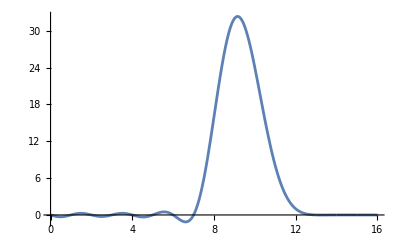

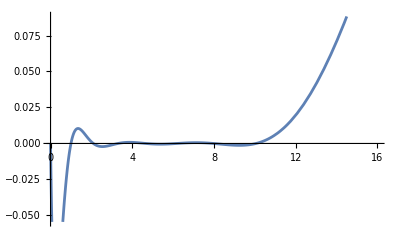

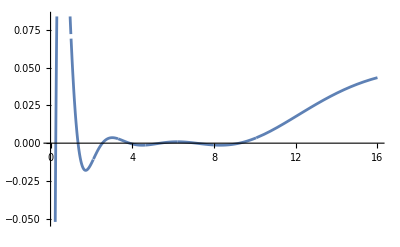

```mathematica
b[x_]:=(3*n)*(1-(1-(1/(3*n)))^x)
f[n_,k_]:=(2^k FactorialPower[n,k])/(k!)
Table[f[5,3*5-x], {x,0,3*5}]
ratio[n_,k_]:=f[n,(3*n)-b[k]]/Binomial[3*n,b[k]]
distr[n_,k_]:=D[ratio[n,x], x]/.x->k
Clear[n]
FactorTerms[FunctionExpand[ratio[n,k]]]
FullSimplify[FunctionExpand[distr[n,k]]]
n=4;
Plot[f[n,3n-k], {k, 0, n^2}]
Plot[ratio[n,k],{k,0,n^2}]
Plot[distr[n,k],{k,0,n^2}]
```

```mathematica
Table[{FactorTerms[FunctionExpand[Binomial[x n,x n-x+1]]],FactorTerms[FunctionExpand[Binomial[x n,x n-x]-n]]}, {x, 0, 9}]
```

{{0,1-n},{1,0},{2 n,2 (-n+n^2)},{3/2 (-n+3 n^2),9/2 (-n^2+n^3)},{4/3 (n-6 n^2+8 n^3),2/3 (-3 n+11 n^2-24 n^3+16 n^4)},{5/24 (-6 n+55 n^2-150 n^3+125 n^4),125/24 (-2 n^2+7 n^3-10 n^4+5 n^5)},{3/5 (2 n-25 n^2+105 n^3-180 n^4+108 n^5),1/10 (-20 n+137 n^2-675 n^3+1530 n^4-1620 n^5+648 n^6)},{7/720 (-120 n+1918 n^2-11025 n^3+29155 n^4-36015 n^5+16807 n^6),343/720 (-36 n^2+232 n^3-735 n^4+1225 n^5-1029 n^6+343 n^7)},{8/315 (45 n-882 n^2+6496 n^3-23520 n^4+44800 n^5-43008 n^6+16384 n^7),2/315 (-315 n+3267 n^2-26264 n^3+108304 n^4-250880 n^5+329728 n^6-229376 n^7+65536 n^8)},{(9 (-560 n+13068 n^2-118188 n^3+548289 n^4-1428840 n^5+2112642 n^6-1653372 n^7+531441 n^8))/4480,(9 (-12176 n^2+118124 n^3-605556 n^4+1818369 n^5-3306744 n^6+3582306 n^7-2125764 n^8+531441 n^9))/4480}}

### Square case

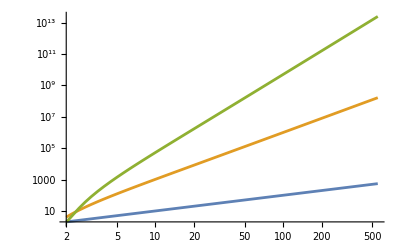

4-6 x+x^2+x^3

-22+33 x-(13 x^2)/2-6 x^3+x^4+x^5/2

```mathematica
l[n_]:=n*Binomial[n^2-n,1]+2*(n-1)*(n-2)
l1[n_]:=n*Binomial[n^2-n,2]+2*(n-2)*(Binomial[n-2,2]+n-2)+2*(n-1)*((n^2-n-3)+(n-3)*(n^2-n-2))+2*(n-1)*Binomial[n-3,2]
LogLogPlot[{n, l[n], l1[n]} ,{n, 2, 550}, PlotRange->Full]
Simplify[l[x]]
Simplify[l1[x]]
```

```mathematica
Simplify[InterpolatingPolynomial[{{6,1966832},{7,13480033},{8,66764072},{9,264081073},{10,884650000},{11,2606370707},{12,6930353940},{13,16942788625},{14,38611859216},{15,82900565717},{16,169083207472},{17,329788111817},{18,618456395728},{19,1120110950839},{20,1966576580444},{21,3357586764777},{22,5589560694064}}, x]]
```

1/120 (779520-1066792 x+327244 x^2+100814 x^3-56635 x^4-5153 x^5+4516 x^6+360 x^7-210 x^8-30 x^9+5 x^10+x^11)

```mathematica
poly1[x_]:=4-6 x+x^2+x^3
poly2[x_]:=1/2 (-44+66 x-13 x^2-12 x^3+2 x^4+x^5)
poly3[x_]:=1/6 (888-1268 x+338 x^2+169 x^3-53 x^4-18 x^5+3 x^6+x^7)
poly4[x_]:=1/24 (-23616+32884 x-9568 x^2-3619 x^3+1666 x^4+278 x^5-118 x^6-24 x^7+4 x^8+x^9)
poly5[x_]:=1/120 (779520-1066792 x+327244 x^2+100814 x^3-56635 x^4-5153 x^5+4516 x^6+360 x^7-210 x^8-30 x^9+5 x^10+x^11)
n=4;
poly1[n]
poly2[n]
poly3[n]
poly4[n]
poly5[n]
Print[Roots[poly1[x]==x, x]]
```

60

390

1452

3422

5260

x==1/3 (-1+22/(1/2 (-173+3 ⅈ √1407))^(1/3)+(1/2 (-173+3 ⅈ √1407))^(1/3))||x==-1/3-(11 (1+ⅈ √3))/(3 (1/2 (-173+3 ⅈ √1407))^(1/3))-1/6 (1-ⅈ √3) (1/2 (-173+3 ⅈ √1407))^(1/3)||x==-1/3-(11 (1-ⅈ √3))/(3 (1/2 (-173+3 ⅈ √1407))^(1/3))-1/6 (1+ⅈ √3) (1/2 (-173+3 ⅈ √1407))^(1/3)

```mathematica
Print[Roots[poly1[x]==0,x]]
Print[Simplify[Roots[poly2[x]==0,x]]]
```

x==-1-√5||x==-1+√5||x==1

3/4+1/2 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))+1/2 √(33/2-(7578+ⅈ √969243)^(1/3)/3^(2/3)-269/(22734+3 ⅈ √969243)^(1/3)-41/(4 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))))+x==0||3/4+1/2 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))+x==1/2 √(33/2-(7578+ⅈ √969243)^(1/3)/3^(2/3)-269/(22734+3 ⅈ √969243)^(1/3)-41/(4 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))))||3/4+1/2 √(33/2-(7578+ⅈ √969243)^(1/3)/3^(2/3)-269/(22734+3 ⅈ √969243)^(1/3)+41/(4 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))))+x==1/2 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))||x==-3/4+1/2 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))+1/2 √(33/2-(7578+ⅈ √969243)^(1/3)/3^(2/3)-269/(22734+3 ⅈ √969243)^(1/3)+41/(4 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))))||x==1

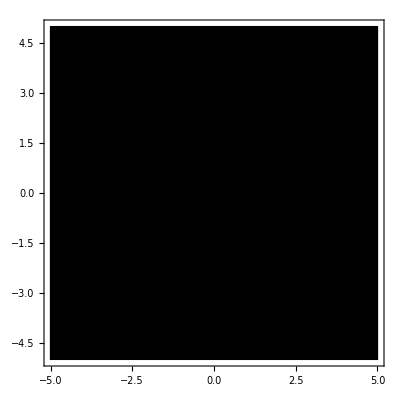

-Graphics3D-

```mathematica
ComplexPlot[poly2[x],{x,-5-5 I,5+5I},PlotLegends->Automatic]
f[x_, y_]:=-22+33 (x+y*I)-(13 (x+y*I)^2/2)-6 (x+y*I)^3+(x+y*I)^4+((x+y*I)^5/2)
xmin=-5;
xmax=5;
ymin=-5;
ymax=5;
Show[Plot3D[Re@f[x,y],{x,xmin,xmax},{y,ymin,ymax},AxesLabel->{"Re(x)","Im(x)","Re(f(x))"},ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reversed"}][Im@f[x,y]]]],Graphics3D[{Gray,Thick,Table[InfiniteLine[{{xmin,y,0},{xmax,y,0}}],{y,ymin,ymax,1/2}],Table[InfiniteLine[{{x,ymin,0},{x,ymax,0}}],{x,xmin,xmax,1}]}]]
```

### Interpolating Direct Formula

```mathematica
Clear[n]
m[n_]:=Sum[Binomial[n,2*k]*CatalanNumber[k], {k, 0, n/2}]
elem[n_]:=(n+2) 3^(n-2)+2 Sum[m[k]*(n-k-2) 3^(n-k-3),{k,0,n-2}]
elem[n_]:=(n+2) 3^(n-2)+2 Sum[(Hypergeometric2F1[1/2-k/2,-k/2,2,4])*(n-k-2) 3^(n-k-3),{k,0,n-2}]
Table[elem[i], {i, 0, 20}]
Simplify[elem[x]]
```

{2/9,1,4,17,68,259,950,3387,11814,40503,136946,457795,1515926,4979777,16246924,52694573,170028792,546148863,1747255194,5569898331,17698806798}

3^(-2+x) (2+x)+2 ∑_(k=0)^(-2+x) 3^(-3-k+x) (-2-k+x) Hypergeometric2F1[1/2-k/2,-k/2,2,4]

```mathematica
poly1[x_]:=FactorTerms[FullSimplify[InterpolatingPolynomial[{{0,1},{1,4},{2,6},{3,4},{4,1}}, x]]]
poly2[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,1},{1,9},{2,36},{3,84},{4,126},{5,126},{6,84},{7,36},{8,9},{9,1}}, x]]]
poly3[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,1},{1,16},{2,120},{3,560},{4,1820},{5,4368},{6,8008},{7,11440},{8,12870},{9,11440},{10,8008},{11,4368},{12,1820},{13,560},{14,120},{15,16},{16,1}}, x]]]
poly4[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,1},{1,25},{2,300},{3,2300},{4,12650},{5,53130},{6,177100},{7,480700},{8,1081575},{9,2042975},{10,3268760},{11,4457400},{12,5200300},{13,5200300},{14,4457400},{15,3268760},{16,2042975},{17,1081575},{18,480700},{19,177100},{20,53130},{21,12650},{22,2300},{23,300},{24,25},{25,1}}, x]]]
poly5[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,1},{1,36},{2,630},{3,7140},{4,58905},{5,376992},{6,1947792},{7,8347680},{8,30260340},{9,94143280},{10,254186856},{11,600805296},{12,1251677700},{13,2310789600},{14,3796297200},{15,5567902560},{16,7307872110},{17,8597496600},{18,9075135300},{19,8597496600},{20,7307872110},{21,5567902560},{22,3796297200},{23,2310789600},{24,1251677700},{25,600805296},{26,254186856},{27,94143280},{28,30260340},{29,8347680},{30,1947792},{31,376992},{32,58905},{33,7140},{34,630},{35,36},{36,1}}, x]]]
poly1[x]
poly2[x]
poly3[x]
poly4[x]
poly5[x]
```

1/4 (4+4 x+15 x^2-8 x^3+x^4)

1/576 (576-7200 x+25100 x^2-22896 x^3+12693 x^4-3564 x^5+510 x^6-36 x^7+x^8)

1/1625702400(1625702400-1215804764160 x+4156695500544 x^2-6061215760896 x^3+5146370947600 x^4-2852007127424 x^5+1104533026184 x^6-309384000576 x^7+64033982161 x^8-9881106112 x^9+1135470460 x^10-96308800 x^11+5926438 x^12-256704 x^13+7412 x^14-128 x^15+x^16)

1/229442532802560000(229442532802560000-49549463099136000000000 x+185296978050262640640000 x^2-306656837992151776051200 x^3+302874454586535835521024 x^4-202243666541959310400000 x^5+97807860068320702872000 x^6-35767222316850064128000 x^7+10181390704210694391280 x^8-2302031871607693500000 x^9+419351157265086260500 x^10-62155289998119846000 x^11+7543746779210668765 x^12-752356243395262500 x^13+61713022317495250 x^14-4156722759469500 x^15+228939340164535 x^16-10236802125000 x^17+367557190000 x^18-10427505000 x^19+228194395 x^20-3712500 x^21+42250 x^22-300 x^23+x^24)

1/40990389067797283140009984000000(40990389067797283140009984000000-10038408561951060713763439523974348800000 x+41937668046233737239110485333612953600000 x^2-79466028639131817234996864583433453568000 x^3+92024493727071140758591850231315752550400 x^4-73795972586728928237785422871735810129920 x^5+43932858607135499690812052763547198193664 x^6-20298907317417991909985982090579135676416 x^7+7506561884655687701151528855439975203840 x^8-2272154554894085017298170130495462022144 x^9+572566498730108536619663232495329864448 x^10-121704347422851382069429466134698642432 x^11+22047686088523681106368743373991414656 x^12-3432067679089062266610129868778656896 x^13+462077288484148304824264246420613088 x^14-54084969433899046932514612603604352 x^15+5525634413379184864400672424761844 x^16-494245481990344474519935227496060 x^17+38787148723854282062093595024575 x^18-2674216463186568375974545122600 x^19+162074669092436483306325518265 x^20-8633032478815161732709248720 x^21+403765063220373408465346620 x^22-16551899579578258399106880 x^23+593160803872274275661580 x^24-18514661256329823248040 x^25+500924382152462098146 x^26-11673440702300955024 x^27+232402792962725550 x^28-3910841504246736 x^29+54849451057772 x^30-629047323648 x^31+5744163864 x^32-40151484 x^33+201687 x^34-648 x^35+x^36)

```mathematica
poly1[x_]:=FactorTerms[FullSimplify[InterpolatingPolynomial[{{2,4},{3,22},{4,60},{5,124},{6,220},{7,354},{8,532},{9,760},{10,1044}}, x]]]
poly2[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{3,59},{4,390},{5,1418},{6,3830},{7,8637},{8,17234},{9,31460},{10,53658},{11,86735},{12,134222},{13,200334},{14,290030},{15,409073}}, x]]]
poly3[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{4,1452},{5,9958},{6,42200},{7,135542},{8,362596},{9,851122},{10,1810168},{11,3563290},{12,6589692},{13,11574126},{14,19466392},{15,31551278},{16,49529780},{17,75612442},{18,112625656}}, x]]]
poly4[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{5,48171},{6,330862},{7,1538918},{8,5573732},{9,16929642},{10,45091226},{11,108423937},{12,240160778},{13,497230517},{14,972830862},{15,1813823056},{16,3244212512},{17,5596183388},{18,9350373402}}, x]]]
poly5[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{6,1966832},{7,13480033},{8,66764072},{9,264081073},{10,884650000},{11,2606370707},{12,6930353940},{13,16942788625},{14,38611859216},{15,82900565717},{16,169083207472},{17,329788111817},{18,618456395728},{19,1120110950839},{20,1966576580444}}, x]]]
poly6[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{7,94850847},{8,649054448},{9,3364850969},{10,14238839294},{11,51559124726},{12,164948309254},{13,476972080825},{14,1267825309002},{15,3137826256285},{16,7304063280756},{17,16119344733941},{18,33947126684342},{19,68589703621580},{20,133553982453866}}, x]]]
poly1[x]
poly2[x]
poly3[x]
poly4[x]
poly5[x]
poly6[x]
```

4-6 x+x^2+x^3

1/2 (-44+66 x-13 x^2-12 x^3+2 x^4+x^5)

1/6 (888-1268 x+338 x^2+169 x^3-53 x^4-18 x^5+3 x^6+x^7)

1/24 (-23616+32884 x-9568 x^2-3619 x^3+1666 x^4+278 x^5-118 x^6-24 x^7+4 x^8+x^9)

1/120 (779520-1066792 x+327244 x^2+100814 x^3-56635 x^4-5153 x^5+4516 x^6+360 x^7-210 x^8-30 x^9+5 x^10+x^11)

1/720 (-30864960+41562504 x-13236764 x^2-3430222 x^3+2228043 x^4+97030 x^5-178480 x^6-1977 x^7+9526 x^8+380 x^9-331 x^10-36 x^11+6 x^12+x^13)

```mathematica
poly1[x_]:=FactorTerms[FullSimplify[InterpolatingPolynomial[{{0,0},{1,0},{2,4},{3,4},{4,1}}, x]]]
poly2[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,0},{1,0},{2,0},{3,17},{4,67},{5,104},{6,81},{7,36},{8,9},{9,1}}, x]]]
poly3[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,0},{1,0},{2,0},{3,0},{4,68},{5,632},{6,2594},{7,6168},{8,9454},{9,9988},{10,7618},{11,4308},{12,1816},{13,560},{14,120},{15,16},{16,1}}, x]]]
poly4[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,0},{1,0},{2,0},{3,0},{4,0},{5,259},{6,4351},{7,34162},{8,165932},{9,556667},{10,1365401},{11,2539513},{12,3682167},{13,4258223},{14,4001349},{15,3098369},{16,1994804},{17,1071617},{18,479282},{19,176976},{20,53125},{21,12650},{22,2300},{23,300},{24,25},{25,1}}, x]]]
poly5[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,950},{7,25060},{8,317102},{9,2558560},{10,14759358},{11,64695152},{12,223592503},{13,624333880},{14,1433343382},{15,2743128692},{16,4428324603},{17,6094699408},{18,7220615444},{19,7426840428},{20,6679532216},{21,5282175608},{22,3686867960},{23,2275803032},{24,1242457649},{25,598838464},{26,253855994},{27,94101080},{28,30256510},{29,8347460},{30,1947786},{31,376992},{32,58905},{33,7140},{34,630},{35,36},{36,1}}, x]]]
poly6[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,3387},{8,128693},{9,2377482},{10,28434398},{11,247304673},{12,1665689983},{13,9034023196},{14,40503284385},{15,152928024312},{16,492946015433},{17,1370692115205},{18,3315050727995},{19,7021671641024},{20,13104689757689},{21,21671059353450},{22,31923016349386},{23,42100944784088},{24,49946796374587},{25,53535734771579},{26,52044487014141},{27,46037853669399},{28,37152428803395},{29,27403160933677},{30,18494458412338},{31,11425387152800},{32,6458436822347},{33,3336822747362},{34,1572883373359},{35,674697753312},{36,262501932917},{37,92250254803},{38,29134377346},{39,8217686994},{40,2054446997},{41,450977712},{42,85900577},{43,13983816},{44,1906884},{45,211876},{46,18424},{47,1176},{48,49},{49,1}}, x]]]
poly1[x]
poly2[x]
poly3[x]
poly4[x]
poly5[x]
```

1/24 (-166 x+243 x^2-86 x^3+9 x^4)

(9953424 x-31279644 x^2+40248308 x^3-27496665 x^4+10651494 x^5-2350026 x^6+291552 x^7-18945 x^8+502 x^9)/362880

1/20922789888000(-336490569254246400 x+1127409710876962560 x^2-1618739915026750848 x^3+1340234906635554384 x^4-722263115740129600 x^5+270052102151435240 x^6-72689238663057016 x^7+14389512273652373 x^8-2117978597020000 x^9+232422190140140 x^10-18915280062224 x^11+1124531200702 x^12-47417636000 x^13+1342669060 x^14-22889912 x^15+177541 x^16)

1/15511210043330985984000000(-298307678156803870881095024640000 x+1123137350768689633740585922560000 x^2-1874467230564580371406607777280000 x^3+1869964560876940761407758850995200 x^4-1263340003788588238905326578718976 x^5+619268712039956935144120658932800 x^6-230012314720755036612958134369600 x^7+66663169677225062255000524037200 x^8-15391336265631458455674072223920 x^9+2873364603192255744268399816300 x^10-438409595841983065299380261100 x^11+55080845465490791263039627075 x^12-5726224068277869336725620560 x^13+493855634113556120475623050 x^14-35348224418771136389804100 x^15+2095919942184623633667325 x^16-102505912314431497670040 x^17+4105134296351411573800 x^18-133132204898001530100 x^19+3439419373674609325 x^20-69080938164907680 x^21+1039173229994050 x^22-11011110755100 x^23+73266563875 x^24-230218824 x^25)

1/92998331697475304366999862037708800000000(14670414454530461307861701392247775041219985408000000 x-60723602704361154443129506123018589979708044083200000 x^2+113800193747193265512090884616706333562780142796800000 x^3-130128173244428676596587365731401746991602102681600000 x^4+102883392529622350389199160644395911827279892992819200 x^5-60299288352622960422917245077743612425444883455918080 x^6+27389965945467350458429461903907536910831735715266560 x^7-9943976320789732434973539299926796312017871745209856 x^8+2951069116398550207640323786203996018911653618433280 x^9-728169844143310344536790055605527581812742619105280 x^10+151371840575597181797502241154414541080568420595200 x^11-26787409873711083856897957771783978604390658809408 x^12+4068970799917266738448221244766440747685877681120 x^13-534047522286565955765689936408780160728450571040 x^14+60884288260415694097866431113657457246433377040 x^15-6054255306792853881180857496581341201309728726 x^16+526776105299809310353543468562536860777131325 x^17-40198250122875624534965022340977296470821550 x^18+2694426593547665101697393842125018717301575 x^19-158759236313980568322521153718625769444040 x^20+8223133292684511392495775072350722950900 x^21-374147017616070655675470822692475315000 x^22+14930766112439011238147585111609414700 x^23-521309170531031374931485380125393460 x^24+15869920839649732041246908256795750 x^25-419260905755960175752188708056420 x^26+9553000949452108965202627300290 x^27-186222718085924487146329020024 x^28+3073031957343269559471290820 x^29-42330278761255766156142520 x^30+477562707477438571226700 x^31-4296629651169363234342 x^32+29636916944374897605 x^33-147129226780870110 x^34+467866408717935 x^35-715617560144 x^36)

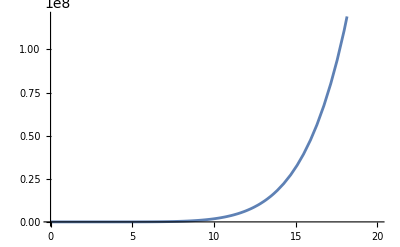

```mathematica
Plot[{ poly3[x]}, {x, 0, 20}, PlotRange->Automatic]
```

```mathematica
p[n_,x_]:=Product[-x+k, {k, 0, n}]/(n!) Sum[(Binomial[n,k]^2 )*(-1)^(k-1)/(x-k),{k,0,n}]
FullSimplify[p[n,x]]
```

(HypergeometricPFQ[{-n,-n,-x},{1,1-x},-1] Pochhammer[1-x,n])/(n!)

```mathematica
p[n_,x_]:=(HypergeometricPFQ[{-n,-n,-x},{1,1-x},-1] Pochhammer[1-x,n])/(n!)
Clear[n]
FactorTerms[Simplify[p[n^2, x]-poly1[n]]]/.x->(n^2 -n-1)
FactorTerms[Simplify[p[2^2, x]]]
FactorTerms[Simplify[p[10, x]]]
```

(HypergeometricPFQ[{-n^2,-n^2,1+n-n^2},{1,2+n-n^2},-1] Pochhammer[2+n-n^2,n^2])/(n^2!)-poly1[n]

1/4 (4+4 x+15 x^2-8 x^3+x^4)

(14400+365760 x-912076 x^2+1198100 x^3-765655 x^4+310690 x^5-78023 x^6+11800 x^7-1045 x^8+50 x^9-x^10)/14400

```mathematica
n=3;
Table[StirlingS2[i,2], {i, 0, 2n}]
```

{0,0,1,3,7,15,31}

```mathematica
poly1[x]
poly2[x]
gcd[x_]:=FactorTerms[PolynomialGCD[poly1[x],poly2[x]]]
gcd1[x_]:=FactorTerms[PolynomialGCD[poly2[x],poly3[x]]]
gcd2[x_]:=FactorTerms[PolynomialGCD[poly3[x],poly4[x]]]
gcd3[x_]:=FactorTerms[PolynomialGCD[poly4[x],poly5[x]]]
gcd[x]
gcd1[x]
gcd2[x]
gcd3[x]
FactorTerms[PolynomialQuotientRemainder[poly2[x], gcd1[x],x]]
hankelMatrix=HankelMatrix[CoefficientList[poly1[x]*Factorial[2],x]]
Column[{poly2[x],Abs[hankelMatrix]^3}]
```

4-6 x+x^2+x^3

1/2 (-44+66 x-13 x^2-12 x^3+2 x^4+x^5)

-13-36 x+12 x^2+10 x^3

1/2 (-1+x)

1/6

1/24

1/120

{3 (-44+66 x-13 x^2-12 x^3+2 x^4+x^5),0}

{{8,-12,2,2},{-12,2,2,0},{2,2,0,0},{2,0,0,0}}

1/2 (-44+66 x-13 x^2-12 x^3+2 x^4+x^5)
{{512,1728,8,8},{1728,8,8,0},{8,8,0,0},{8,0,0,0}}

```mathematica
{remainder,coeffs}=PolynomialReduce[poly2[x],{poly1[x], gcd[x], gcd1[x]},x];
If[remainder===0,Print["The target polynomial can be formed with the set of polynomials."];
Print["Coefficients: ",coeffs],Print["The target polynomial cannot be formed with the set of polynomials."]]
```

The target polynomial cannot be formed with the set of polynomials.

```mathematica
GroebnerBasis[{ poly3[x], poly4[x]},x]
```

{-6 x+11 x^2-6 x^3+x^4}

### Get distribution from polynomials😣

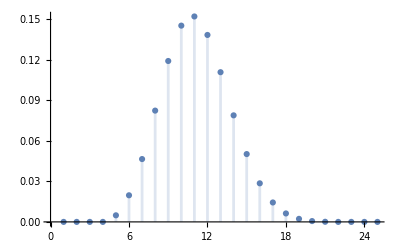

```mathematica
distr1[x_]:=poly4[x]/Binomial[Exponent[poly4[k],k],x]
DiscretePlot[distr1[x]-distr1[x-1], {x, 0, Exponent[poly4[k],k], 1}]
```

### Normal distribution for final number of elements

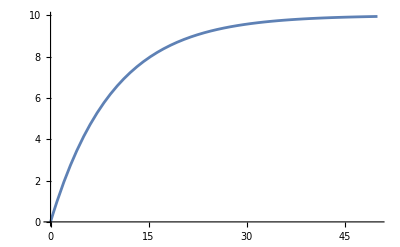

```mathematica
n=5;
b[x_]:=(2*n)*(1-(1-(1/(2*n)))^x)
Plot[b[x], {x,0,50}]
```

## Proportion calculations

```mathematica
n=19
b[x_]:=(n^2)*(1-(1-(1/n^2))^x);
Plot[Binomial[n^2, b[x]], {x, 0, n^2}, PlotRange->Full]
```

19

-Graphics-

```mathematica
b[x_]:=1-(1-(1-(1/n^2))^x);
```

10

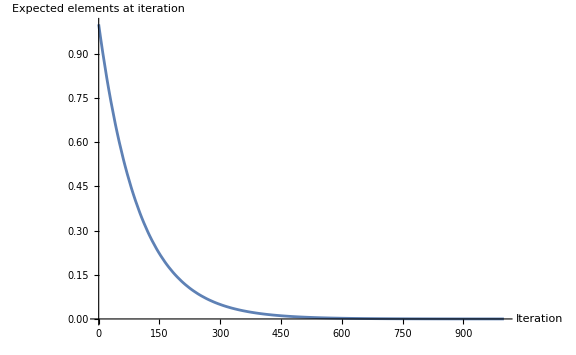

```mathematica
n=10
Plot[{b[x]},{x,0,10n^2},PlotRange->All,AxesLabel->{"Iteration","Expected elements at iteration"},ImageSize->Large]
```

```mathematica
Clear[n]
Integrate[b[x], {x, 0, q}]
D[b[x], x]
```

(-1+(1-1/n^2)^(x/10))/Log[1-1/n^2]

(1-1/n^2)^x Log[1-1/n^2]

```mathematica
area[x_]:=n^2 (x-(-1+(1-1/n^2)^x)/Log[1-1/n^2])
```

```mathematica
n=30
k=n^3
N[area[k]/(k*b[k])]
```

30

27000

0.966685

```mathematica
Clear[n]
N[Limit[area[k]/(k*b[k]),n->Infinity]]
```

$Aborted

## Analysis using p[k,j,n,m] expected number of elements

### Calculate n exponent (1D case)

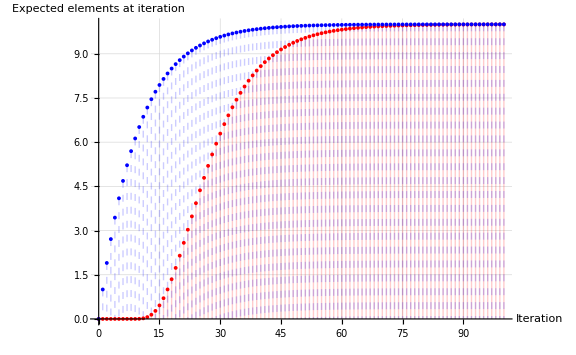

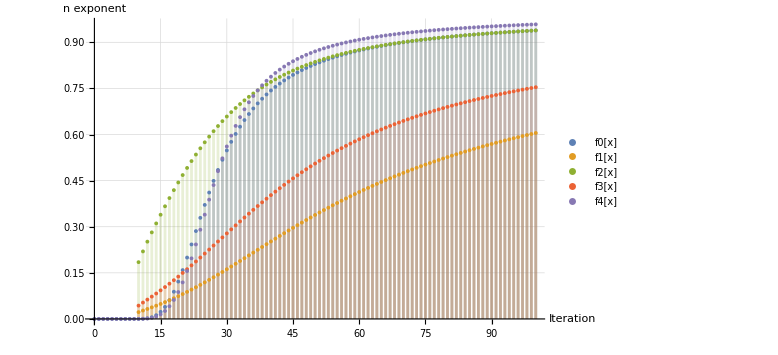

```mathematica
n=10;
b[x_]:=n(1-(1-(1/n))^x);
p[k_,j_,n_,m_]:=StirlingS2[k,j]*Factorial[n*m]/(Factorial[(n*m)-j]*(n*m)^k)
g[x_]:=(-2/1)LogIntegral[x]
nexp0[x_]:=1*(g[p[x,n,n,1]])/(g[p[x,n,n,1]]+1)
nexp1[x_]:=1*(g[p[x,n,n,1]])/(g[p[x,n,n,1]] +p[x,n,n,1]*n)
nexp2[x_]:=1*(g[p[x,n,n,1]])/(g[p[x,n,n,1]] +p[x,n,n,1])
nexp3[x_]:=1*(g[p[x,n,n,1]])/(g[p[x,n,n,1]] +p[x,n,n,1]*n/2)
nexp4[x_]:=2/Pi *ArcTan[g[p[x,n,n,1]]]
DiscretePlot[{p[x,n,n,1]*n,b[x]},{x,0,10*n},PlotRange->Full, PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}},AxesLabel->{"Iteration","Expected elements at iteration"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
DiscretePlot[{nexp0[x], nexp1[x], nexp2[x], nexp3[x], nexp4[x]},{x,0, 10*n },PlotRange->Full,AxesLabel->{"Iteration","n exponent"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}, PlotLegends->{"f0[x]","f1[x]","f2[x]","f3[x]","f4[x]"}]
```

### Calculate insertion complexity

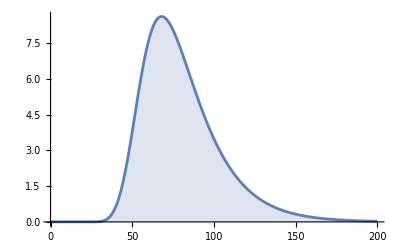

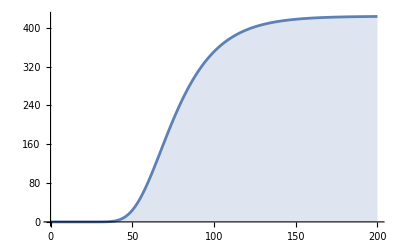

```mathematica
n=20;
ins[x_]:=(1-p[x,n,n,1])*2 n*((g[p[x,n,n,1]])/(g[p[x,n,n,1]]+1))
DiscretePlot[{ins[x]},{x, 0, 10n}]
DiscretePlot[{Sum[ins[x], {x, 0, q}]},{q, 0, 10n}]
```

### Get the max point

```mathematica
n=10;
puntoEstab:=Module[{result},result=NMaximize[{ins[x], x>0},x];
xOptimal=x/. result[[2]];xOptimal]
puntoEstab
Plot[{puntoEstab},{n, 6, 50}]
(*Plot[{NIntegrate[ins[x], {x, 0, puntoEstab}]},{n, 2, 4}]*)
```

13.3418

-Graphics-

### Sum insertion complexity until the algorithm ends

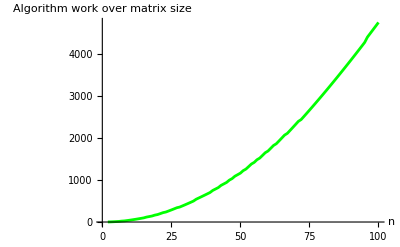

```mathematica
LaunchKernels[];
Clear[n];
points=ParallelTable[{n, Sum[ins[x],{x,0,(n*HarmonicNumber[n])}]},{n, 2, 100}];
ListLinePlot[{points},PlotRange->All,AxesLabel->{"n","Algorithm work over matrix size"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
CloseKernels[];
```

### Fit the sum points

{-0.958245,2.04967}

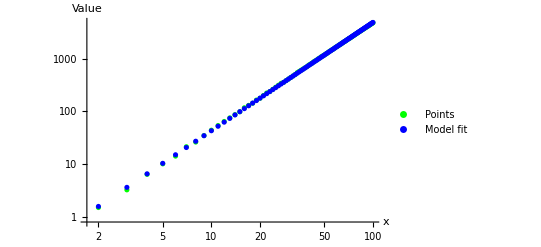

```mathematica
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x];
fittedLine=linearModel["Function"];
linearModel["BestFitParameters"]
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,100}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right]]
```

2.02165
FittedModel[0.430256 x       ]

0.430256 #1^2.02165&

| DF | SS | MS
Model | 2 | 4.59439×10^8 | 2.2972×10^8
Error | 97 | 4822.42 | 49.7157
Uncorrected Total | 99 | 4.59444×10^8 | 
Corrected Total | 98 | 2.02044×10^8 |

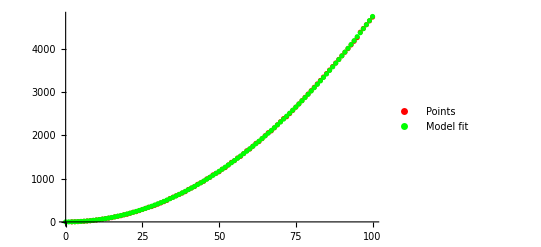

```mathematica
nonlinearModel=NonlinearModelFit[points,a*x^c ,{a,c},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,100}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right]]
```

## Data science section

```mathematica
data=Import["C:\\Users\\danie\\Desktop\\JavaProjects\\practica-eda\\PracticaEDA\\t_values_1D.txt","Table"];
```

```mathematica
points:=data
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x, IncludeConstantBasis->True];
fittedLine=linearModel["Function"];
linearModel
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,1000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right]]
```

FittedModel[2.25421 + 1.78792 Log[x]]

-Graphics-

FittedModel[…]

#1^3.51141&

| DF | SS | MS
Model | 1 | 1.16907×10^23 | 1.16907×10^23
Error | 35911 | 1.43512×10^22 | 3.99632×10^17
Uncorrected Total | 35912 | 1.31258×10^23 | 
Corrected Total | 35911 | 5.71212×10^22 |

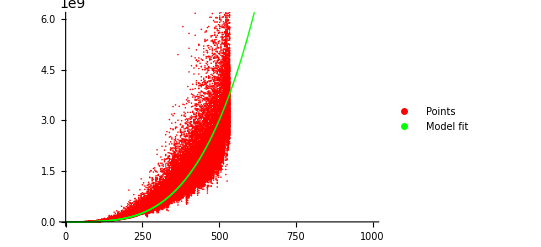

```mathematica
nonlinearModel=NonlinearModelFit[points,x^a ,{a},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,1000}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right]]
```